```mathematica
BASEHEALTH=85;
```

```mathematica
(*This statement creates and sets a global variable for the harvest of a given run.*)
(*harvestProfile=MakeHarvestProfile;*)

(*Below are the functions for LifeEnjoyment given health and investment, Health Regained given an investment, and Health Degeneration per round.
Each is preceded by its associated constants.*)
alpha=0.028;
beta = 0.5;
mu=0.5;
c=500;
LifeEnjoyment[investment_,currentHealth_]:= c*(beta*(currentHealth/100)+mu)*(1-E^((-1)*alpha*investment));
r = 100;
gamma = 78.9;
sigma = 0.025;
HealthRegained[investment_]:=gamma*((1-E^((-1)*sigma*investment))/(1+E^((-1)*sigma*(investment-r))));
HealthDegeneration[currentHealth_,currentRound_]:=currentHealth-(15+currentRound);
```

```mathematica
(*Given the current round and current health, this function evaluates the current harvestProfile and returns the effective harvest of a round.
It should be noted that the current health and current round can be adjusted in this function without affecting the harvestProfile*)
HarvestCurrentRound[currentHealth_,currentRound_]:=
Module[{currentHarvest,harvestTimer,evHarvest},
evHarvest=9.32;
If[currentHealth≥0,
currentHarvest=10*evHarvest*(currentHealth/100),
currentHarvest=0];
Return[currentHarvest]
];
```

```mathematica
CalculateRandomSpendingProfile:=Module[{normalValue,values},
values = Table[N@RandomChoice[IntegerPartitions[1000,{3}]]/1000,9]
];


CalculateHealthAndStorageSpending:=Module[{values},
values = Table[N@RandomChoice[IntegerPartitions[1000,{3}]]/1000,9]
];

HealthSpendingPerRound[healthSpendingStrategy_,BASEHEALTH_]:=
Module[{healthPerRoundWithSpending,currentHarvest,health},
health=BASEHEALTH;
healthPerRoundWithSpending = Table[
If[HealthDegeneration[health,i]>0,
currentHarvest = HarvestCurrentRound[health,i],
currentHarvest=0];
If[health>0&&currentHarvest>0,
health = Min[HealthDegeneration[health,i]+HealthRegained[healthSpendingStrategy[[i]]*currentHarvest],100],
health=0
]
,{i,1,Length[healthSpendingStrategy]}];
Return[healthPerRoundWithSpending]
];

LifeEnjoymentSpendingPerRound[lifeEnjoymentSpendingStrategy_,health_]:=
Module[{currentHarvest,lifeEnjoyment,lifeEnjoymentPerRoundWithSpending},
lifeEnjoyment=0;
currentHarvest=0;
lifeEnjoymentPerRoundWithSpending = Table[
If[health[[i]]>0,
currentHarvest = HarvestCurrentRound[health[[i]],i],
currentHarvest=0];
lifeEnjoyment+=LifeEnjoyment[lifeEnjoymentSpendingStrategy[[i]]*currentHarvest,health[[i]]]
,{i,1,Length[lifeEnjoymentSpendingStrategy]}
];
Return[lifeEnjoymentPerRoundWithSpending]
];

StorageSpendingPerRound[savingsStrategy_,earningsPerRound_]:=
Module[{savingsPerRound,savings},
savingsPerRound = Table[
savings=savingsStrategy[[i]]*earningsPerRound[[i]]
,{i,1,Length[savingsStrategy]}
];
Return[savingsPerRound]
];

earningPerRoundAfterSavings[savingsStrategy_]:=
Module[{evHarvest,savings,earningsWithSavings,earnings},
evHarvest=9.32;
savings=0;
earningsWithSavings=Table[
If[i==1,
earnings=10*evHarvest-(savingsStrategy[[i]]*93.2),
savings=10*evHarvest*savingsStrategy[[i-1]];
earnings=(10*evHarvest+savings)-(10*evHarvest*savingsStrategy[[i]])
]
,{i,1,9}];
Return[earningsWithSavings]
];

SpendingPerRound[healthAndStorageSpendingStrategy_,BASEHEALTH_]:=
Module[{currentHarvest,lifeEnjoymentSpendingProfile,lifeEnjoyment,health,storage},
lifeEnjoymentSpendingProfile = 1-healthAndStorageSpendingStrategy[[All,2]];
health = HealthSpendingPerRound[healthAndStorageSpendingStrategy[[All,1,1]],BASEHEALTH];
lifeEnjoyment = LifeEnjoymentSpendingPerRound[lifeEnjoymentSpendingProfile,health];
storage=StorageSpendingPerRound[healthAndStorageSpendingStrategy[[All,1,2]],health];
Return[Transpose[{health,lifeEnjoyment,storage}]]
];


NewSpendingPerRound[healthAndStorageSpendingStrategy_,BASEHEALTH_]:=
Module[{evHarvest,lifeEnjoymentSpendingStrategy,lifeEnjoyment,health,storage,savings,earnings,lifeTime,healthSpendingStrategy,savingsStrategy},
lifeEnjoymentSpendingStrategy = healthAndStorageSpendingStrategy[[All,2]];
healthSpendingStrategy=healthAndStorageSpendingStrategy[[All,1]];
savingsStrategy=healthAndStorageSpendingStrategy[[All,3]];
evHarvest=93.2;
savings=0;
health=BASEHEALTH;
lifeEnjoyment=0;
lifeTime=Table[
If[i==1,
(*If Round 1*)
earnings=evHarvest*health/100;
savings=earnings*savingsStrategy[[i]];
If[health>0&&earnings>0,
health = Min[HealthDegeneration[health,i]+HealthRegained[healthSpendingStrategy[[i]]*earnings],100],
health=0
];
lifeEnjoyment+=LifeEnjoyment[lifeEnjoymentSpendingStrategy[[i]]*earnings,health];
{health,lifeEnjoyment,savings},


(*If Not Round 1*)
earnings=(evHarvest*health/100)+savings;
savings=earnings*savingsStrategy[[i]];
If[health>0&&earnings>0,
health = Max[0,Min[HealthDegeneration[health,i]+HealthRegained[healthSpendingStrategy[[i]]*earnings],100]],
health=0
];
lifeEnjoyment+=LifeEnjoyment[lifeEnjoymentSpendingStrategy[[i]]*earnings,health];
{health,lifeEnjoyment,savings}
]
,{i,1,9}];
Return[lifeTime]
];
```

```mathematica
MutationDistribution=TruncatedDistribution[{0,1},NormalDistribution[μ,σ]];
Mutation[healthSpendingStrategy_,mutationDeviation_]:=
Module[{chanceOfMutation,newSpendingStrat,inputStrategy},
inputStrategy=healthSpendingStrategy;
newSpendingStrat=Table[
chanceOfMutation=RandomReal[{0,1}];
Which[
chanceOfMutation≤0.1,
inputStrategy[[i]]=RandomVariate[MutationDistribution/.{μ->inputStrategy[[i]],σ->mutationDeviation[[i]]}],
chanceOfMutation>0.1,
inputStrategy[[i]]
]
,{i,1,Length[healthSpendingStrategy]}
];
Return[newSpendingStrat]
];

BankMutation[SpendingStrategy_,mutationDeviation_]:=
Module[{chanceOfMutation,newSpendingStrat,inputStrategy,temp,normalValues,newHealth,newLE,newSavings,rand},
inputStrategy=SpendingStrategy;
newSpendingStrat=Table[
chanceOfMutation=RandomReal[{0,1}];
Which[
chanceOfMutation≤0.1,
temp=inputStrategy[[i,1]];
newHealth=RandomVariate[MutationDistribution/.{μ->inputStrategy[[i,1]],σ->mutationDeviation[[i]]}];
rand=RandomReal[{0,1}];
If[temp-newHealth>0,
If[rand<.5,
newLE=inputStrategy[[i,2]]+(temp-newHealth);
newSavings=inputStrategy[[i,3]],
newSavings=inputStrategy[[i,3]]+(temp-newHealth);
newLE=inputStrategy[[i,2]];
];,
If[rand≥.5,
newLE=inputStrategy[[i,2]]+(temp-newHealth);
newSavings=inputStrategy[[i,3]];
If[newLE<0,
newSavings+=newLE;
newLE=0;
],
newSavings=inputStrategy[[i,3]]+(temp-newHealth);
newLE=inputStrategy[[i,2]];
If[newSavings<0,
newLE+=newSavings;
newSavings=0;
];
];
];
{newHealth,newLE,newSavings},
chanceOfMutation>0.1,
inputStrategy[[i]]
]
,{i,1,Length[SpendingStrategy]}
];
Return[newSpendingStrat]
];
```

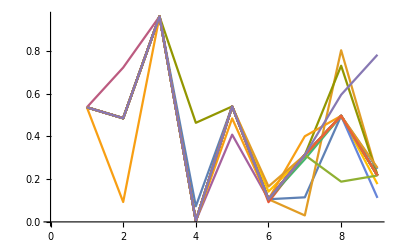

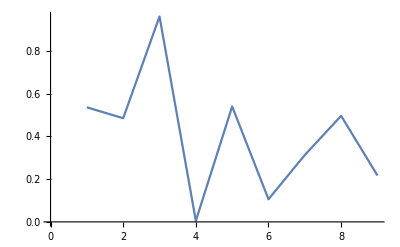

```mathematica
test =CalculateRandomSpendingProfile;
mutatedProfiles = Table[
Mutation[test,{.3,.3,.3,.3,.3,.3,.3,.3,.3}]
,{20}];
ListLinePlot[mutatedProfiles]
ListLinePlot[test]
```

```mathematica
a=CalculateRandomSpendingProfile;
spend=NewSpendingPerRound[a,85];
a//MatrixForm
b=BankMutation[a,{.3,.3,.3,.3,.3,.3,.3,.3,.3}];
b//MatrixForm
```

(0.829 | 0.153 | 0.018
0.504 | 0.405 | 0.091
0.491 | 0.397 | 0.112
0.584 | 0.35 | 0.066
0.649 | 0.21 | 0.141
0.823 | 0.174 | 0.003
0.457 | 0.277 | 0.266
0.445 | 0.295 | 0.26
0.713 | 0.233 | 0.054)

(0.556716 | 0.153 | 0.290284
0.504 | 0.405 | 0.091
0.491 | 0.397 | 0.112
0.584 | 0.35 | 0.066
0.649 | 0.21 | 0.141
0.823 | 0.174 | 0.003
0.457 | 0.277 | 0.266
0.708575 | 0.0314251 | 0.26
0.67634 | 0.233 | 0.0906598)

# Simluation

#### Contains tournament selection and implementation specifics not covered in functions.

```mathematica
(*n is the number of profiles generated*)
populationSize=150;
generations=400;
(*Allocate and Populate the two arrays for populations. One is the initial which is perpetuated, the second is a storage array
which stores the values to be passed on during computation*)
best={{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}};
initialProfilePopulation=Table[
CalculateRandomSpendingProfile,
{populationSize}];
resultingPopulation=ConstantArray[0,populationSize];
(*Randomly Select 2 profiles from the population of profiles, and evaluate their corresponding health and payout profiles*)
Do[
Do[
profileOne =RandomChoice[initialProfilePopulation];
profileTwo =RandomChoice[initialProfilePopulation];
spendingOne=NewSpendingPerRound[profileOne,BASEHEALTH];
spendingTwo=NewSpendingPerRound[profileTwo,BASEHEALTH];

(*Tournament Selection. Randomly Select 2 Health Spending profiles, pass on the more fit profile*)
resultingPopulation[[j]]=
Which[
spendingOne[[9,2]]≥spendingTwo[[9,2]],
BankMutation[profileOne,{.3,.3,.3,.3,.3,.3,.3,.3,.3}],
spendingOne[[9,2]]≤spendingTwo[[9,2]],
BankMutation[profileTwo,{.3,.3,.3,.3,.3,.3,.3,.3,.3}]
];
(*If a specific profile is better than the current best observed profile, store it as the new best profile*)
If[spendingOne[[9,2]]>NewSpendingPerRound[best,BASEHEALTH][[9,2]],
best=profileOne;
];
If[spendingTwo[[9,2]]>NewSpendingPerRound[best,BASEHEALTH][[9,2]],
best=profileTwo;
];
,{j,1,populationSize}
];
initialProfilePopulation=resultingPopulation,
{generations}
];
```

(90.0315 | 112.699 | 0.
93.5207 | 297.075 | 0.
95.0854 | 541.497 | 0.
95.2332 | 807.982 | 0.
93.8073 | 1075.93 | 2.1101
88.1438 | 1410.57 | 0.
76.059 | 1755.5 | 0.
58.6438 | 2066.23 | 1.17582
34.7108 | 2332.12 | 0.)

(0.877922 | 0.122078 | 0
0.79578 | 0.20422 | 0
0.715033 | 0.284967 | 0
0.681777 | 0.318223 | 0
0.652205 | 0.324021 | 0.0237738
0.504253 | 0.495747 | 0
0.33441 | 0.66559 | 0
0.212572 | 0.770841 | 0.0165872
0.00320076 | 0.996799 | 0)

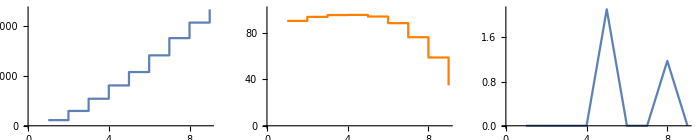

```mathematica
Text[Style[NewSpendingPerRound[best,BASEHEALTH]//MatrixForm,TextAlignment->Center]]
Text[Style[best//MatrixForm,TextAlignment->Center]]
LifeEnjoymentLine=ListLinePlot[NewSpendingPerRound[best,BASEHEALTH][[All,2]],InterpolationOrder->0];
HealthOverTimeLine=ListLinePlot[NewSpendingPerRound[best,BASEHEALTH][[All,1]],InterpolationOrder->0,PlotStyle->Orange,PlotRange->{0,100}];
BankLine=ListLinePlot[NewSpendingPerRound[best,BASEHEALTH][[All,3]],InterpolationOrder->1];
HealthSpendingValues=ListLinePlot[best[[All,1]],InterpolationOrder->0,PlotStyle->Red];
GraphicsRow[{LifeEnjoymentLine,HealthOverTimeLine,BankLine}]
```